# HW 3 - ASTR510

## Daniel George

## Q1

## Burger’s Equation

```mathematica
(∂u(x,t))/(∂t)+u(x,t) (∂u(x,t))/(∂x)==μ (∂^2 u(x,t))/(∂x^2)
```

### Initial condition

```mathematica
g[x_]=.5 Sin[Pi x]+Sin[2Pi x];
```

## a)

## FTCS scheme

```mathematica
ftcs=(v[k][l + 1] - v[k][l])/ht + 
   v[k][l](v[k+1][l] - v[k - 1][l])/
    (2hx) == μ (v[k+1][l] + v[k - 1][l]-2 v[k][l])/
    (hx^2);ftcs//TraditionalForm
```

(v(k)(l+1)-v(k)(l))/ht+(v(k)(l) (v(k+1)(l)-v(k-1)(l)))/(2 hx)==(μ (v(k-1)(l)-2 v(k)(l)+v(k+1)(l)))/hx^2

### Solving for v(k)(l+1)

```mathematica
Solve[ftcs,v[k][l+1]][[1,1]]//TraditionalForm
```

v(k)(l+1)→1/(2 hx^2)(ht hx v(k-1)(l) v(k)(l)-ht hx v(k)(l) v(k+1)(l)+2 ht μ v(k-1)(l)-4 ht μ v(k)(l)+2 ht μ v(k+1)(l)+2 hx^2 v(k)(l))

### Function to advance by one time-step using FTCS

```mathematica
FTCS=Function[{v,hx,ht,μ},ArrayPad[ArrayFilter[1/(2 hx^2)(ht #[[1]] (2 μ+hx #[[2]])+2 ht μ #[[3]]+#[[2]] (2 hx^2-4 ht μ-ht hx #[[3]]))&,v,1][[2;;-2]],1]];
```

## b)

### Function to initialize array given g(x) and hx

```mathematica
init=Function[{g,hx},g/@Range[0,1,hx]];
```

### Function to iterate upto 1 second given g(x), hx, ht and μ

The function stops iterating if the solution starts to blow up.

```mathematica
iter=Function[{f,hx,ht,μ},NestWhileList[FTCS[#,hx,ht,μ]&,init[f,hx],Max@Abs@#<1.5&,1,Floor[1/ ht]]];
```

## c)

### Function to find largest stable time-step using bisection method

```mathematica
fLdt=Function[{f,hx,μ},
Module[{dtL,dtR,dtC},dtL=dtR=hx;
While[Length@iter[f,hx,dtR,μ]==Floor[1/dtR]+1,dtR+=.5dtR;];While[Length@iter[f,hx,dtL,μ]!=Floor[1/dtL]+1,dtL-=.5 dtL;];
While[Abs[dtL-dtR]>10^-7,
dtC=.5(dtL+dtR);
If[Length@iter[f,hx,dtC,μ]<Floor[1/dtC]+1,dtR=dtC,dtL=dtC]];
dtL]];
```

### Computing largest time-step for various grid spacings

```mathematica
dtdx=Transpose[{#,fLdt[g,#,.01]&/@#}]&@Range[.005,.015,.0005];
```

### Plot of largest time-step vs grid spacing

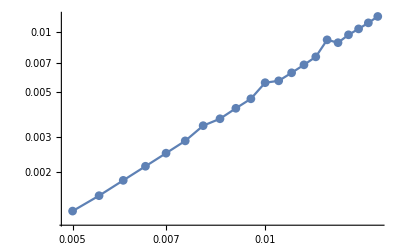

```mathematica
ListLogLogPlot[dtdx,Joined->True,PlotMarkers->Automatic]
```

### Best fit curve to the above log-log plot

```mathematica
fit[x_]=Fit[Log@dtdx,{1,x},x]
```

4.20807+2.05448 x

This means that dt is proportional to dx^2

### Exact relationship between dt and dx

```mathematica
fit[x_]=Fit[dtdx,{x^2},x]
```

52.9196 x^2

Therefore the CFL criterion is that dt is approximately equal to 50 dx^2

## d)

### Plot of u(x,t) at t = 0 and t = 1

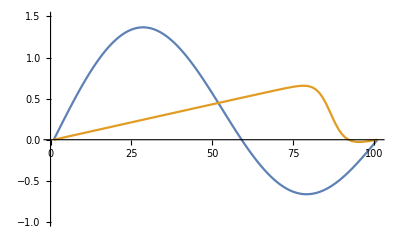

```mathematica
With[{d=iter[g,.01,.1fLdt[g,.01,.01],.01]},ListLinePlot[{d[[1]],d[[-1]]},PlotRange->{-1,1.5}]]
```

We can see that the solution is becoming more steeper with increase in time. This could eventually cause a shock to form.